# One patch, with and without effect of microbes on pollinators

This creates phase plane and time series plots for one-plant model with and without feedbacks between microbes and pollinators, and with low and high yeast dispersal rates (keeping bacterial dispersal rates constant).

#### Load package and set working directory:

```mathematica
Needs["EcoEvo`"];
SetDirectory[NotebookDirectory[]];
SetDirectory[ParentDirectory[]<> "/_figures/_raw-nb"];
```

#### Define model in EcoEvo:

```mathematica
SetModel[{Pop[Y]->{Equation:>dy disp[B, h, S0, L0] Y (1-Y-B)-m Y, Range:>Interval[{0,1}], Color->RGBColor["#FFCC33"]},
Pop[B]->{Equation:>(db0+db disp[B, h, S0, L0]) B (1-Y-B)-m B, Range:>Interval[{0,1}], Color->RGBColor["#333399"]},
Parameters:>{dy >= 0,db0 >= 0, db >= 0,h>= 0,L0>= 0,m>= 0, S0>=0}}];
disp[B_, h_, S0_, L0_]:=Module[{P}, 
P = S0^h / (S0^h + B^h); 
P / (L0 + P)
];
```

#### Create functions used throughout and define unchanging parameter values:

```mathematica
Pvec[S0_, h_, L0_, t_, simBFun_]= disp[simBFun[t], h, S0, L0];
timeseriesPlot[maxt_?NumericQ, hiStart_?NumericQ, loStart_?NumericQ]:=Module[{sim1, sim2, simp1, simp2, p1, p2, pp1, pp2}, 
sim1 = EcoSim[{Y -> hiStart, B->loStart}, maxt];
sim2 = EcoSim[{Y -> loStart, B->hiStart}, maxt];
simp1 = PlotDynamics[sim1, AxesLabel-> None];
simp2 = PlotDynamics[sim2, AxesLabel-> None];
p1 = Plot[Pvec[S0, h, L0, t, sim1[[2]][[2]]], {t, 0, maxt}, PlotStyle->Directive[Thick,Gray, Dashed],AspectRatio->0.85, PlotRange -> {Automatic, {0, 1}}];
p2 = Plot[Pvec[S0, h, L0, t, sim2[[2]][[2]]], {t, 0, maxt}, PlotStyle->Directive[Thick,Gray, Dashed],AspectRatio->0.85, PlotRange -> {Automatic, {0, 1}}];
pp1 = Show[p1, simp1, PlotRange -> {Automatic, {0, 1}},AxesOrigin->{0,0}];
pp2 = Show[p2, simp2, PlotRange -> {Automatic, {0, 1}},AxesOrigin->{0,0}];
GraphicsRow[{pp1, pp2}, ImageSize-> Medium]
];
db = 0.4;
db0 = 0.3;
m = 0.1;S0 = 0.4;
```

## Phase planes and time series plots

### No feedbacks, high yeast dispersal

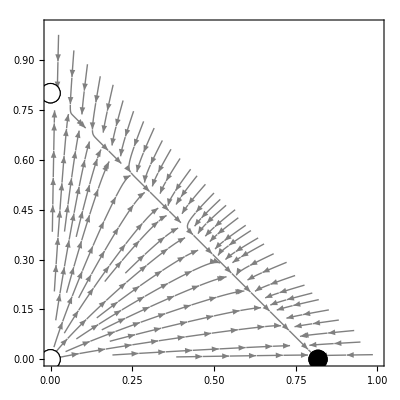

```mathematica
Clear[h, dy, L0];
h = 0.0; dy = 1.1; L0 = 0.5;
p = PlotEcoPhasePlane[ {Y,0,1},{B,0,1}, 
IsoclineStyle->{Opacity[0], Opacity[0]},
RuleListPlotOpts->{StableMarker->{Graphics[{Black,Disk[{0,0}]},ImageSize->20,AlignmentPoint->{0,0}]},
UnstableMarker-> {Graphics[{EdgeForm[{Black}],FaceForm[White],Disk[{0,0}]},ImageSize->20,AlignmentPoint->{0,0}]}}, 
FrameLabel -> None,
RegionFunction->Function[{Y, B},0 <= Y+B <= 1]]
Export[File["1patch-h0-dy1.1-phase.pdf"],p];
Clear[p];
```

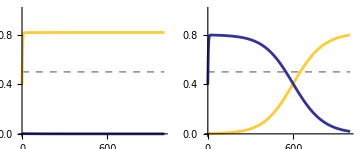

```mathematica
Clear[h, dy, L0];
h = 0.0; dy = 1.1; L0 = 0.5;
combinedPlot = timeseriesPlot[1000, 0.4, 0.001]
Export[File["1patch-h0-dy1.1-timeseries.pdf"],combinedPlot];
Clear[combinedPlot];
```

### No feedbacks, low yeast dispersal

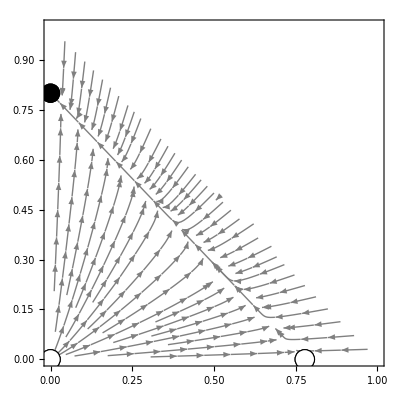

```mathematica
Clear[h, dy, L0];
h = 0.0; dy = 0.9; L0 = 0.5;
p = PlotEcoPhasePlane[ {Y,0,1},{B,0,1}, 
IsoclineStyle->{Opacity[0], Opacity[0]},
RuleListPlotOpts->{StableMarker->{Graphics[{Black,Disk[{0,0}]},ImageSize->20,AlignmentPoint->{0,0}]},
UnstableMarker-> {Graphics[{EdgeForm[{Black}],FaceForm[White],Disk[{0,0}]},ImageSize->20,AlignmentPoint->{0,0}]}}, 
FrameLabel -> None,
RegionFunction->Function[{Y, B},0 <= Y+B <= 1]]
Export[File["1patch-h0-dy0.9-phase.pdf"],p];
Clear[p];
```

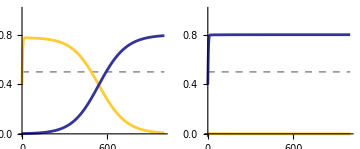

```mathematica
Clear[h, dy, L0];
h = 0.0; dy = 0.9; L0 = 0.5;
combinedPlot = timeseriesPlot[1000, 0.4, 0.001]
Export[File["1patch-h0-dy0.9-timeseries.pdf"],combinedPlot];
Clear[combinedPlot];
```

### With feedbacks, high yeast dispersal

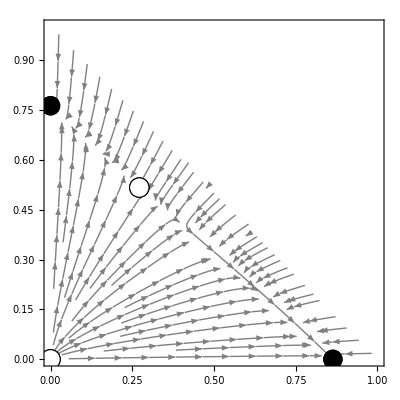

```mathematica
Clear[h, dy, L0];
h = 2.0; dy = 1.1; L0 = 0.5;
p = PlotEcoPhasePlane[ {Y,0,1},{B,0,1}, 
IsoclineStyle->{Opacity[0], Opacity[0]},
RuleListPlotOpts->{StableMarker->{Graphics[{Black,Disk[{0,0}]},ImageSize->20,AlignmentPoint->{0,0}]},
UnstableMarker-> {Graphics[{EdgeForm[{Black}],FaceForm[White],Disk[{0,0}]},ImageSize->20,AlignmentPoint->{0,0}]}}, 
FrameLabel -> None,
RegionFunction->Function[{Y, B},0 <= Y+B <= 1]]
Export[File["1patch-h2-dy1.1-phase.pdf"],p];
Clear[p];
```

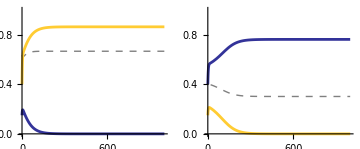

```mathematica
Clear[h, dy, L0];
h = 2.0; dy = 1.1; L0 = 0.5;
combinedPlot = timeseriesPlot[1000, 0.4, 0.15]
Export[File["1patch-h2-dy1.1-timeseries.pdf"],combinedPlot];
Clear[combinedPlot];
```

### With feedbacks, low yeast dispersal

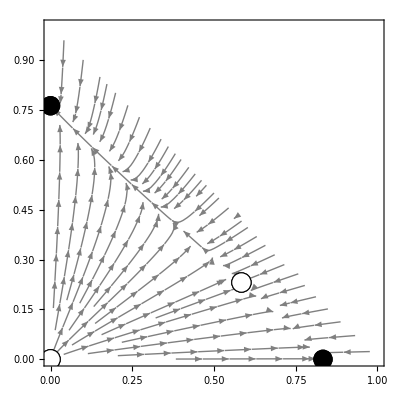

```mathematica
Clear[h, dy, L0];
h = 2.0; dy = 0.9; L0 = 0.5;
p = PlotEcoPhasePlane[ {Y,0,1},{B,0,1}, 
IsoclineStyle->{Opacity[0], Opacity[0]},
RuleListPlotOpts->{StableMarker->{Graphics[{Black,Disk[{0,0}]},ImageSize->20,AlignmentPoint->{0,0}]},
UnstableMarker-> {Graphics[{EdgeForm[{Black}],FaceForm[White],Disk[{0,0}]},ImageSize->20,AlignmentPoint->{0,0}]}}, 
FrameLabel -> None,
RegionFunction->Function[{Y, B},0 <= Y+B <= 1]]
Export[File["1patch-h2-dy0.9-phase.pdf"],p];
Clear[p];
```

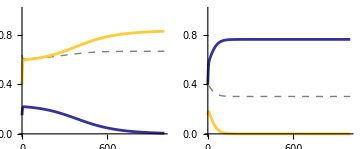

```mathematica
Clear[h, dy, L0];
h = 2.0; dy = 0.9; L0 = 0.5;
combinedPlot = timeseriesPlot[1000, 0.4, 0.15]
Export[File["1patch-h2-dy0.9-timeseries.pdf"],combinedPlot];
Clear[combinedPlot];
```